```mathematica
Series[1/2/λ/l^2(1-Sqrt[1-4λ(1-(rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ) z^4+(k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ])^2 z^6)]),{λ,0,1}]
```

(3-3 rp^4 z^4-16 l^2 π rp^2 z^4 μ^2+2 k^2 l^2 rp^4 z^6 μ^2)/(3 l^2)+((-64/3 l^2 π rp^2 z^4 μ^2+8/3 k^2 l^2 rp^4 z^6 μ^2+1/4 (-4+4 rp^4 z^4+64/3 l^2 π rp^2 z^4 μ^2-8/3 k^2 l^2 rp^4 z^6 μ^2)^2) λ)/(4 l^2)+O[λ]^2

```mathematica
Expand[(3-3 (1/zp)^4 z^4-16 l^2 π (1/zp)^2 z^4 μ^2+2 k^2 l^2 (1/zp)^4 z^6 μ^2)/(3 l^2)/.{k->Sqrt[8Pi],l->1}]
```

1-z^4/zp^4+(16 π z^6 μ^2)/(3 zp^4)-(16 π z^4 μ^2)/(3 zp^2)

```mathematica
Expand[1-(1+zp^2μ^2)(z/zp)^4+zp^2μ^2 (z/zp)^6]
```

1-z^4/zp^4+(z^6 μ^2)/zp^4-(z^4 μ^2)/zp^2

```mathematica
(*expanding the equation of motion*)
```

```mathematica
Series[-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k-> Sqrt[8 Pi],l->1},{λ,0,0}]
```

(-(2 q2 μ z[t])/zp^2+(3 √3 zp^4 z'[t]^2)/(z[t]^2 (zp^2-z[t]^2) (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4) √((9 zp^8-18 zp^4 z[t]^4-96 π zp^6 μ^2 z[t]^4+96 π zp^4 μ^2 z[t]^6+9 z[t]^8+96 π zp^2 μ^2 z[t]^8+256 π^2 zp^4 μ^4 z[t]^8-96 π μ^2 z[t]^10-512 π^2 zp^2 μ^4 z[t]^10+256 π^2 μ^4 z[t]^12-9 zp^8 z'[t]^2)/(zp^4 (zp^2-z[t]^2) (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4))))+(√((9 zp^8-18 zp^4 z[t]^4-96 π zp^6 μ^2 z[t]^4+96 π zp^4 μ^2 z[t]^6+9 z[t]^8+96 π zp^2 μ^2 z[t]^8+256 π^2 zp^4 μ^4 z[t]^8-96 π μ^2 z[t]^10-512 π^2 zp^2 μ^4 z[t]^10+256 π^2 μ^4 z[t]^12-9 zp^8 z'[t]^2)/(zp^4 (zp^2-z[t]^2) (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4))))/(√3 z[t]^2)-(6 √3 zp^4 z[t]^2 (6+32 π zp^2 μ^2-48 π μ^2 z[t]^2) z'[t]^2)/((zp^2-z[t]^2)^2 (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4)^2 √(-((-9 zp^8+18 zp^4 z[t]^4+96 π zp^6 μ^2 z[t]^4-96 π zp^4 μ^2 z[t]^6-9 z[t]^8-96 π zp^2 μ^2 z[t]^8-256 π^2 zp^4 μ^4 z[t]^8+96 π μ^2 z[t]^10+512 π^2 zp^2 μ^4 z[t]^10-256 π^2 μ^4 z[t]^12+9 zp^8 z'[t]^2)/(zp^4 (zp^2-z[t]^2) (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4)))))-(2 z[t]^2 (-3-16 π zp^2 μ^2+24 π μ^2 z[t]^2) (9 zp^8-18 zp^4 z[t]^4-96 π zp^6 μ^2 z[t]^4+96 π zp^4 μ^2 z[t]^6+9 z[t]^8+96 π zp^2 μ^2 z[t]^8+256 π^2 zp^4 μ^4 z[t]^8-96 π μ^2 z[t]^10-512 π^2 zp^2 μ^4 z[t]^10+256 π^2 μ^4 z[t]^12+9 zp^8 z'[t]^2))/(√3 zp^4 (-zp^2+z[t]^2)^2 (-3 zp^2-3 z[t]^2+16 π μ^2 z[t]^4)^2 √((9 zp^8-18 zp^4 z[t]^4-96 π zp^6 μ^2 z[t]^4+96 π zp^4 μ^2 z[t]^6+9 z[t]^8+96 π zp^2 μ^2 z[t]^8+256 π^2 zp^4 μ^4 z[t]^8-96 π μ^2 z[t]^10-512 π^2 zp^2 μ^4 z[t]^10+256 π^2 μ^4 z[t]^12-9 zp^8 z'[t]^2)/(zp^4 (-zp^2+z[t]^2) (-3 zp^2-3 z[t]^2+16 π μ^2 z[t]^4))))-(3 √3 zp^4 z''[t])/(z[t] (zp^2-z[t]^2) (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4) √((9 zp^8-18 zp^4 z[t]^4-96 π zp^6 μ^2 z[t]^4+96 π zp^4 μ^2 z[t]^6+9 z[t]^8+96 π zp^2 μ^2 z[t]^8+256 π^2 zp^4 μ^4 z[t]^8-96 π μ^2 z[t]^10-512 π^2 zp^2 μ^4 z[t]^10+256 π^2 μ^4 z[t]^12-9 zp^8 z'[t]^2)/(zp^4 (zp^2-z[t]^2) (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4))))+(9 √3 zp^4 z'[t] (-(2 z[t]^3 (6+32 π zp^2 μ^2-48 π μ^2 z[t]^2) z'[t])/(3 zp^4)-(6 zp^4 z[t]^3 (6+32 π zp^2 μ^2-48 π μ^2 z[t]^2) z'[t]^3)/((zp^2-z[t]^2)^2 (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4)^2)-(6 zp^4 z'[t] z''[t])/((zp^2-z[t]^2) (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4))))/(2 z[t] (zp^2-z[t]^2) (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4) ((9 zp^8-18 zp^4 z[t]^4-96 π zp^6 μ^2 z[t]^4+96 π zp^4 μ^2 z[t]^6+9 z[t]^8+96 π zp^2 μ^2 z[t]^8+256 π^2 zp^4 μ^4 z[t]^8-96 π μ^2 z[t]^10-512 π^2 zp^2 μ^4 z[t]^10+256 π^2 μ^4 z[t]^12-9 zp^8 z'[t]^2)/(zp^4 (zp^2-z[t]^2) (3 zp^2+3 z[t]^2-16 π μ^2 z[t]^4)))^(3/2)))+O[λ]^1==0

```mathematica
(*qcrit expanded*)
```

```mathematica
Series[Sqrt[1-zs^4/zp^4+(16 π zs^6 μ^2)/(3 zp^4)-(16 π zs^4 μ^2)/(3 zp^2)]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2],{λ,0,0}]
```

(zp √(((zp^2-zs^2) (3 zp^2+3 zs^2-16 π zs^4 μ^2))/zp^4))/(√3 (zp-zs) zs μ)+O[λ]^1

```mathematica
Series[Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh,{λ,0,0}]
```

(√3)/(k l zh)+O[λ]^1

```mathematica
f[z_,zp_,μ_]:=1-z^4/zp^4+(16 π z^6 μ^2)/(3 zp^4)-(16 π z^4 μ^2)/(3 zp^2);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=(zp √(((zp^2-zs^2) (3 zp^2+3 zs^2-16 π zs^4 μ^2))/zp^4))/(√3 (zp-zs) zs μ);
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=(√3)/(k l zh);
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/fz1[t1,q1,μ1,zh1,zs1]/f[fz1[t1,q1,μ1,zh1,zs1],zh1,μ1]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[f[fz1[t1,q1,μ1,zh1,zs1],zh1,μ1]-1/f[fz1[t1,q1,μ1,zh1,zs1],zh1,μ1]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
```

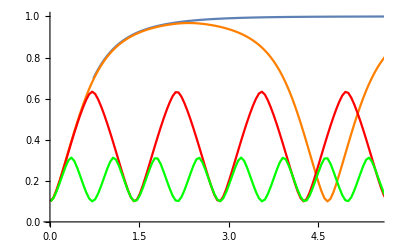

```mathematica
Show[
ListLinePlot[Table[{i,Abs[fz1[i,0,1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[fz1[i,0.95qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fz1[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Red],

ListLinePlot[Table[{i,Abs[fz1[i,7qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.125],1,0.125]]},{i,0.01,7,0.05}],PlotStyle->Green],PlotRange->{{0.01,5.5},{0,1}},AxesOrigin->{0,0}
]
```

```mathematica
Table[{i,Abs[pz[i,0.1qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]//Log},{i,0.01,7,0.05}]
```

{{0.01,-0.0264966},{0.06,1.61225},{0.11,1.96546},{0.16,2.08198},{0.21,2.1056},{0.26,2.0653},{0.31,1.96235},{0.36,1.80043},{0.41,1.59492},{0.46,1.36585},{0.51,1.12889},{0.56,0.892553},{0.61,0.659001},{0.66,0.424414},{0.71,0.175238},{0.76,-0.129699},{0.81,-0.647148},{0.86,-2.83289},{0.91,-0.915003},{0.96,-0.349116},{1.01,-0.0883074},{1.06,0.0938214},{1.11,0.250815},{1.16,0.398855},{1.21,0.542135},{1.26,0.678384},{1.31,0.799014},{1.36,0.887933},{1.41,0.922885},{1.46,0.883014},{1.51,0.757572},{1.56,0.54164},{1.61,0.214659},{1.66,-0.30861},{1.71,-1.50417},{1.76,-1.24267},{1.81,-0.234005},{1.86,0.244233},{1.91,0.544991},{1.96,0.739122},{2.01,0.843181},{2.06,0.861821},{2.11,0.807136},{2.16,0.700606},{2.21,0.563776},{2.26,0.411503},{2.31,0.251223},{2.36,0.0841432},{2.41,-0.095325},{2.46,-0.306414},{2.51,-0.613077},{2.56,-1.30056},{2.61,-2.35637},{2.66,-0.869183},{2.71,-0.443882},{2.76,-0.20031},{2.81,-0.0105863},{2.86,0.15969},{2.91,0.32133},{2.96,0.476215},{3.01,0.620124},{3.06,0.74204},{3.11,0.823352},{3.16,0.841273},{3.21,0.77817},{3.26,0.62702},{3.31,0.380577},{3.36,0.00351407},{3.41,-0.649379},{3.46,-3.40405},{3.51,-0.784855},{3.56,-0.0634535},{3.61,0.337527},{3.66,0.598136},{3.71,0.761145},{3.76,0.835574},{3.81,0.827434},{3.86,0.752958},{3.91,0.634852},{3.96,0.492638},{4.01,0.338355},{4.06,0.177063},{4.11,0.00775024},{4.16,-0.178759},{4.21,-0.411775},{4.26,-0.796434},{4.31,-1.93922},{4.36,-1.49209},{4.41,-0.68131},{4.46,-0.350942},{4.51,-0.133526},{4.56,0.0474322},{4.61,0.214376},{4.66,0.374095},{4.71,0.526181},{4.76,0.664089},{4.81,0.774},{4.86,0.835019},{4.91,0.825023},{4.96,0.73035},{5.01,0.546091},{5.06,0.258971},{5.11,-0.18984},{5.16,-1.06988},{5.21,-1.92409},{5.26,-0.457281},{5.31,0.103916},{5.36,0.444297},{5.41,0.667027},{5.46,0.797301},{5.51,0.840459},{5.56,0.805679},{5.61,0.71267},{5.66,0.583922},{5.71,0.436363},{5.76,0.279316},{5.81,0.115599},{5.86,-0.0582645},{5.91,-0.256432},{5.96,-0.524425},{6.01,-1.04412},{6.06,-4.95539},{6.11,-1.07552},{6.16,-0.537164},{6.21,-0.264677},{6.26,-0.0650633},{6.31,0.109348},{6.36,0.273332},{6.41,0.430636},{6.46,0.578664},{6.51,0.708361},{6.56,0.803077},{6.61,0.840417},{6.66,0.800379},{6.71,0.673398},{6.76,0.454323},{6.81,0.119333},{6.86,-0.429406},{6.91,-1.80693},{6.96,-1.12425}}

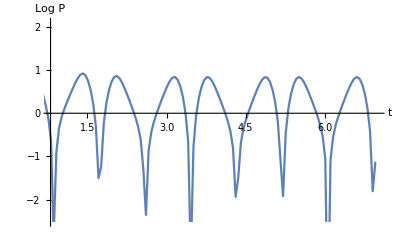

```mathematica
Show[
ListLinePlot[Table[{i,Abs[pz[i,0.1qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.01],1,0.01]]//Log},{i,0.01,7,0.05}]],
PlotRange->{{0.8,7},All},AxesOrigin->{0.8,0},AxesLabel->{t,Log P}
]
```